-Graphics-

# Wolfram Language

## Structured Data

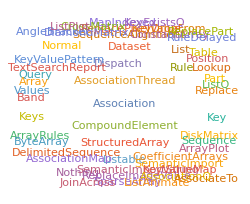

-Graphics-

## Objectives

The following types of structured data will be described:

List

PackedArray

SparseArray

Association

Each of the following sections will explain how and when a data type should be used.

## List ({..})

Lists are general objects that represent collections of arbitrary expressions. They work best when the length of the collection rarely changes.

Here is an example of a basic list:

```mathematica
list = List[a, b, c, d]
```

{a,b,c,d}

You’ll notice that the input was entered using the verbose FullForm version of List, but the output was given using the short form with brackets. Typically one will use the short form for input as well:

```mathematica
list = {a, b, c, d}
```

{a,b,c,d}

The output is the same. It is always possible to see the FullForm of an expression:

```mathematica
FullForm[list]
```

List[a,b,c,d]

The elements of a list can contain any Wolfram Language™ expression:


{x,-Graphics3D-,-Graphics-}

```mathematica
{x, Region@Cone[], Plot[Sin[x], {x, 0, 2Pi}]}
```

In particular, an element of a list can be another list. This is how matrices are constructed:

```mathematica
matrix = {{a, b}, {c, d}}
```

{{a,b},{c,d}}

Use MatrixForm to view the nested list object as a matrix:

```mathematica
x=matrix//MatrixForm
```

(a | b
c | d)

## List: Element extraction

### Part ([[...]])

#### FullForm

The most common method to extract parts of a list is to use Part, which has the short form [[ ]]. For example, given the list:

```mathematica
list = {1, 2, 3, 4, 5, 6, 7, 8, 9, 10};
```

The second element of the list can be obtained with:

```mathematica
Part[list, 2]
```

2

The above example used the FullForm of Part, but it is much more convenient and readable to use the short form with brackets:

```mathematica
list[[2]]
```

2

It is also possible to use special characters instead of double brackets:

```mathematica
list⟦2⟧
```

2

```mathematica
list⟦2⟧
```

2

This last version is nice because it distinguishes the double brackets for Part from nested function calls like f[g[x]], and will be used in the remainder of this talk.

#### Part specifications

When a positive index is used in Part, the count starts from the beginning. It is also possible to specify the part using a negative index, in which case the count starts at the end of the list. For example, here is the second to last element:

```mathematica
list⟦-2⟧
```

9

To obtain multiple parts, use a list as the argument:

```mathematica
list⟦{1, 3}⟧
```

{1,3}

Another very useful part specification is Span, with the short form ;;. The following Span specification takes the second through the sixth elements in steps of 2.

```mathematica
Span[2,6,2]
```

2;;6;;2

Using Span in a Part specifiction:

```mathematica
{1,2,3,4,5,6,7,8}⟦2;;6;;2⟧
```

{2,4,6}

Finally, it is possible to use UpTo in a span specification. Typically, specifying an index that is out of range (e.g., an index that is longer than the length of the list), you will get an error:

```mathematica
{1,2,3,4,5,6,7,8}⟦2;;10⟧
```

Part::take: Cannot take positions 2 through 10 in {1,2,3,4,5,6,7,8}.

{1,2,3,4,5,6,7,8}⟦2;;10⟧

Using UpTo allows the specification of a span that would be out of range:

```mathematica
{1,2,3,4,5,6,7,8}⟦2;;UpTo[10]⟧
```

{2,3,4,5,6,7,8}

#### Nested part specifications

For nested lists (e.g., a matrix), you can use Part to extract a nested part (or list of parts). Here is a matrix:

```mathematica
matrix = {{a,b,c},{d,e,f},{g,h,i}};
matrix //MatrixForm
```

(a | b | c
d | e | f
g | h | i)

To get the second element of the third list (row):

```mathematica
matrix⟦3,2⟧
```

h

In this case it is also possible to nest Part specifications to obtain the same answer:

```mathematica
matrix⟦3⟧⟦2⟧
```

h

Get the second column:

```mathematica
matrix⟦All,2⟧
```

{b,e,h}

Get a submatrix:

```mathematica
matrix⟦{1,3},{1,3}⟧
```

{{a,c},{g,i}}

### Extract

It is possible to use Extract and as well to extract parts from a list. For example, the first two nested list examples above using Extract:

```mathematica
Extract[list, 2]
```

2

```mathematica
Extract[matrix,{3,2}]
Extract[matrix,{All,2}]
```

h

{b,e,h}

### Pitfalls

Nested Part specfications are not always equivalent to a single Part specification. For example:

```mathematica
matrix⟦{1,3}, 2⟧
matrix⟦{1,3}⟧⟦2⟧
```

{b,h}

{g,h,i}

Extract is not the same as Part. In particular, Extract interprets nested lists of indices as a request to extract multiple parts. For example:

```mathematica
Extract[matrix,{{1,3},{1,3}}]
```

{c,c}

Here each {1,3} specification extracts the same part from the matrix.

## List: Modification

#### Part

In the previous slide, Part was used to obtain parts of a list. It is also possible to use Part on the left hand side of a Set operation:

```mathematica
list
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
list⟦5⟧=x;
list
```

{1,2,3,4,x,6,7,8,9,10}

```mathematica
matrix//MatrixForm
```

(a | b | c
d | e | f
g | h | i)

```mathematica
matrix⟦2,2⟧=Region@Cone[];
matrix //MatrixForm
```

(a | b | c
d | -Graphics3D- | f
g | h | i)

Just like before, it is also possible to use a list to modify multiple values.

Setting all of the elements to a single value:

```mathematica
list
```

{1,2,3,4,x,6,7,8,9,10}

```mathematica
list⟦{1,5}⟧=y;
list
```

{y,2,3,4,y,6,7,8,9,10}

Setting each element to a different value:

```mathematica
list⟦{2,6}⟧={Pi, E};
list
```

{y,π,3,4,y,ⅇ,7,8,9,10}

Finally, one can also use Span as before:

```mathematica
matrix⟦All, 2⟧={10,100,1000};
matrix //MatrixForm
```

(a | 10 | c
d | 100 | f
g | 1000 | i)

#### ReplacePart

ReplacePart can also be used to create a new list with parts that have been modified:

```mathematica
ReplacePart[list, 5->"NEW"]
```

{y,π,3,4,NEW,ⅇ,7,8,9,10}

Notice that list has not been modified:

```mathematica
list
```

{y,π,3,4,y,ⅇ,7,8,9,10}

#### Join, Flatten, Append

Use Join to join lists together:

```mathematica
list1 = {a, b, c};
list2 = {d, e, f};
Join[list1, list2]
```

{a,b,c,d,e,f}

Here are 2 matrices:

```mathematica
(matrix1 = {{1,2},{3,4}})//MatrixForm
(matrix2 = {{a,b},{c,d}})//MatrixForm
```

(1 | 2
3 | 4)

(a | b
c | d)

The default level specification stacks the two matrices on top of each other:

```mathematica
Join[matrix1, matrix2]//MatrixForm
```

(1 | 2
3 | 4
a | b
c | d)

Using a level specification of 2 joins the two matrices side by side:

```mathematica
Join[matrix1, matrix2, 2]//MatrixForm
```

(1 | 2 | a | b
3 | 4 | c | d)

It is also possible to use Append/Prepend to increase or decrease the size of a list:

```mathematica
Append[matrix1, x]
```

{{1,2},{3,4},x}

Flatten can be used to convert a nested list into an unnested list:

```mathematica
Flatten[matrix1]
```

{1,2,3,4}

An interesting application Flatten is to transpose an array. For example:

```mathematica
matrix1//MatrixForm
Flatten[matrix1,{{2},{1}}]//MatrixForm
```

(1 | 2
3 | 4)

(1 | 3
2 | 4)

## List: Construction

#### Table

Table is the basic tool to create a list:

```mathematica
Table[i^2, {i, 10}]
```

{1,4,9,16,25,36,49,64,81,100}

Create a matrix:

```mathematica
Table[i j, {i, 3}, {j, 3}]//MatrixForm
```

(1 | 2 | 3
2 | 4 | 6
3 | 6 | 9)

Use a list iterator:

```mathematica
Table[i+1, {i, {1,5,10}}]
```

{2,6,11}

#### Range

Range is basically a specialized Table idiom for creating an arithmetic progression:

```mathematica
Range[10]
Range[5,11]
Range[10,6,-1]
```

{1,2,3,4,5,6,7,8,9,10}

{5,6,7,8,9,10,11}

{10,9,8,7,6}

#### Array

Array can be used to generate an array with a function f applied to the indices:

```mathematica
Array[f, 5]
```

{f[1],f[2],f[3],f[4],f[5]}

It is convenient for creating a symbolic matrix:

```mathematica
Array[Subscript[m,##]&, {3,3}]//MatrixForm
```

(m_(1,1) | m_(1,2) | m_(1,3)
m_(2,1) | m_(2,2) | m_(2,3)
m_(3,1) | m_(3,2) | m_(3,3))

#### ConstantArray

Use ConstantArray to create an array where every element is the same:

```mathematica
ConstantArray[1, {3,3}]
```

{{1,1,1},{1,1,1},{1,1,1}}

Of course, it is also possible to use Table, although the syntax is slightly different:

```mathematica
Table[1, {3},{3}]
```

{{1,1,1},{1,1,1},{1,1,1}}

One of the nice features of lists are that operations on lists typically occur element-wise. For example:

```mathematica
list = {1, 2,3};
list+1
```

{2,3,4}

This is much more convenient than doing something like:

```mathematica
Table[list⟦i⟧+1, {i, 3}]
```

{2,3,4}

Other examples:

```mathematica
Sin[{1.,2.,.3}]
```

{0.841471,0.909297,0.29552}

```mathematica
list^2+list
```

{2,6,12}

As will be demonstrated in the next topic, operations on entire lists in this manner not only produces more readable code, it can be much faster.

## List: Performance considerations

Copying or creating lists has a timing that is linear in the length of the list. This means that creating a list by repeatedly appending elements actually has a timing that is quadratic in the length of the list.

```mathematica
makeList[n_] := Module[{tmp={}},
	Do[AppendTo[tmp, i], {i, n}];
	tmp
]
```

The above function just creates a list of integers:

```mathematica
makeList[10]
```

{1,2,3,4,5,6,7,8,9,10}

A comparison of the timing complexity of makeList with Range:

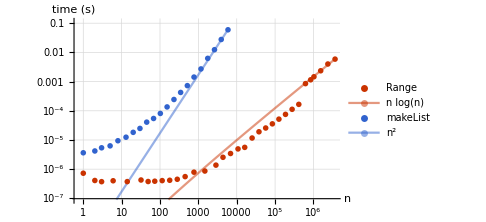

```mathematica
Needs["GeneralUtilities`"]
BenchmarkPlot[{Range,makeList}, Identity,"IncludeFits"->True]
```

Later in this talk Association will be introduced, which has a timing complexity logarithmic in the length of the list for this kind of operation.

An alternative to using an append operation is to preallocate an array, and then to use in-place modification to update the values. This is because in-place modification does not create a copy of the array:

```mathematica
inPlace[n_]:=Module[{tmp=ConstantArray[0, n]},
Do[tmp⟦i⟧=i, {i, n}];
tmp
]
```

Example output:

```mathematica
inPlace[10]
```

{1,2,3,4,5,6,7,8,9,10}

Benchmark:

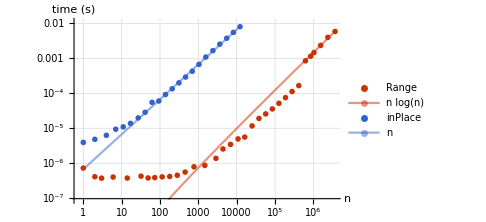

```mathematica
Needs["GeneralUtilities`"]
BenchmarkPlot[{Range,inPlace}, Identity,"IncludeFits"->True]
```

## List: Summary

General container for arbitrary expressions.

Optimal when size of list doesn’t change.

## PackedArray

The basic List structure described above has a memory footprint quite a bit larger than what one might expect based on the size of the data structure in a language like C. For this reason, packed arrays were introduced into the language when the elements of the array all have the same type, with supported types being Integer, Real, and Complex. To work with packed arrays, it will be convenient to load the Developer utilities package:

```mathematica
Needs["Developer`"]
```

## PackedArray: Memory

An example of a packed array (generated automatically by RandomReal) and the corresponding unpacked array:

Reals:

```mathematica
packedRealArray = RandomReal[1, 10^6];
unpackedRealArray = FromPackedArray @ packedRealArray;
```

Integers:

```mathematica
packedIntegerArray = RandomInteger[1, 10^6];
unpackedIntegerArray = FromPackedArray @ packedIntegerArray;
```

Complex numbers:

```mathematica
packedComplexArray = RandomComplex[1+I, 10^6];
unpackedComplexArray = FromPackedArray @ packedComplexArray;
```

Comparison of the memory footprint:

```mathematica
ByteCount[packedRealArray]
ByteCount[unpackedRealArray]
```

8000144

24000080

```mathematica
ByteCount[packedIntegerArray]
ByteCount[unpackedIntegerArray]
```

8000144

24000080

```mathematica
ByteCount[packedComplexArray]
ByteCount[unpackedComplexArray]
```

16000144

64000080

## PackedArray: Speed

Many functions in the Wolfram Language have special support for packed arrays. For example:

```mathematica
Sin[packedRealArray]; //AbsoluteTiming
Sin[unpackedRealArray]; //AbsoluteTiming
```

{0.00153,Null}

{0.008496,Null}

The important feature here is that one computes with the array as a whole. Doing the above computation in a Table would be much slower:

```mathematica
Table[Sin[r], {r, packedRealArray}]; //AbsoluteTiming
```

{0.044286,Null}

## PackedArray: Appearance

Mathematica attempts to utilize packed arrays behind the scenes whenever possible, so that you typically do not have to worry about them. In fact, typically there is no visual difference between packed arrays and unpacked arrays. Compare:

```mathematica
unpackedArray = {1,2,3}
packedArray = Range[3]
```

{1,2,3}

{1,2,3}

The output appears identical, however, the first array is not packed, while the second one is:

```mathematica
PackedArrayQ @ unpackedArray
PackedArrayQ @ packedArray
```

False

True

It is very helpful to have this model of packed arrays in mind in case your code appears to be slower than expected.

## PackedArray: Comparing Packed vs Unpacked computation

Here are simple examples of an unpacked array and a packed array:

```mathematica
unpackedArray = {1, 2, 3}
packedArray = Range[3]
```

{1,2,3}

{1,2,3}

The function TracePrint can reveal what happens when a packed array is involved in a numerical computation, for example, adding 1 to each element. Here is the unpacked version:

```mathematica
TracePrint[1+unpackedArray, _Plus]
```

1+unpackedArray

1+{1,2,3}

1+1

1+2

1+3

{2,3,4}

Notice how 1 is added to each element of the list by the top level evaluator. Compare this to adding 1 to the packed array:

```mathematica
TracePrint[1+packedArray, _Plus]
```

1+packedArray

1+{1,2,3}

{2,3,4}

With a packed array, Wolfram Language is able to bypass the top level evaluator and use special purpose code to add 1 to each element of the array.

This is the key feature of the speed up that using packed array provides.

## PackedArray: Debugging

You can make use of PackedArrayQ to determine if an array is packed. For example, here is a packed array:

```mathematica
array = RandomReal[1, 10]
```

{0.284419,0.737054,0.583942,0.329188,0.654136,0.728102,0.579392,0.829302,0.772772,0.78131}

Suppose you want to replace the fifth element with 0:

```mathematica
array⟦5⟧=0
```

0

Since 0 is an integer, while the array consisted of real numbers, array is no longer packed, since the elements no longer have the same type:

```mathematica
PackedArrayQ@array
```

False

One other useful tool is to turn on packing messages:

```mathematica
On["Packing"]
```

Here is another packed array:

```mathematica
array = RandomReal[1, 10];
```

Replace the fifth element with 0 again:

```mathematica
array⟦5⟧=0
```

FromPackedArray::punpack1: Unpacking array with dimensions {10}.

0

Turn off packing messages:

```mathematica
Off["Packing"]
```

## PackedArray: Summary

Packed arrays use less memory and are faster.

Packed arrays are automatically used where possible.

Unexpected memory usage or speed inefficiencies typically mean that a packed array may have become unpacked.

## SparseArray

When working with large arrays where most of the elements have a default value and comparatively few have non-default values, it is useful to be able to only specify the positions of the non-default values, with all other elemens taken to have the default value. The resulting object will use much less memory, and list operations with SparseArray objects with sufficiently high sparsity will be much faster than corresponding operations will dense arryas. In the Wolfram Language, you can use a SparseArray object instead of a List to represent such arrays.

In contrast to packed arrays, SparseArray objects have a different appearance, but have been designed to behave identically to ordinary lists. Just like operations on packed arrays bypass top level evaluations for list operations, similarly operations on SparseArray objects also bypass top level evaluations.

## SparseArray: Construction

### Basic rules

The basic method for constructing a SparseArray object is to give a list of pos->value rules:

```mathematica
sparse=SparseArray[{1->a, 3->b}]
```

SparseArray[…]

Here is the usual List version:

```mathematica
Normal[sparse]
```

{a,0,b}

By default the sparse array that is constructed is as small as possible based on the positions specified, and uses 0 as the default value.

Another example that creates a matrix instead of a vector:

```mathematica
sparse = SparseArray[{{1,1}->a, {1,3}->b, {2,3}->c}, {3,3}, 1]
```

SparseArray[…]

```mathematica
sparse//MatrixForm
```

(a | 1 | b
1 | 1 | c
1 | 1 | 1)

You'll notice that this time the default element is 1, and the size has been explicitly specified to be 3×3 and not 2×3 as might be expected based on the positions that have specified.

One can obtain the rules used to create a SparseArray object by using ArrayRules:

```mathematica
ArrayRules[sparse]
```

{{1,1}→a,{1,3}→b,{2,3}→c,{_,_}→1}

### Patterned rules

An important feature of constructing SparseArray objects using rules is that the position specifications can be patterns:

```mathematica
SparseArray[{{_, _?EvenQ}->1, {_?OddQ,_}->2}, {4,4}]//MatrixForm
```

(2 | 1 | 2 | 1
0 | 1 | 0 | 1
2 | 1 | 2 | 1
0 | 1 | 0 | 1)

Note that the first rule that matches is used to fill in the position values. In this case the EvenQ rule took precedence. Changing the order of the rules will change the output:

```mathematica
SparseArray[{{_?OddQ,_}->2,{_, _?EvenQ}->1}, {4,4}]//MatrixForm
```

(2 | 2 | 2 | 2
0 | 1 | 0 | 1
2 | 2 | 2 | 2
0 | 1 | 0 | 1)

Now the OddQ rule takes precedence.

### Band

One final constructor is Band, with a syntax that can be a bit complicated. Here is a basic example:

```mathematica
SparseArray[{Band[{1,2}]->x},{3,3}]//MatrixForm
```

(0 | x | 0
0 | 0 | x
0 | 0 | 0)

In the above example, every element on the {1,2} diagonal is the same. It is possible to use a List as the right hand side of the rule:

```mathematica
SparseArray[{Band[{1,2}]->{x,y}},{3,3}]//MatrixForm
```

(0 | x | 0
0 | 0 | y
0 | 0 | 0)

A final example of creating a matrix with a nonzero submatrix:

```mathematica
SparseArray[{Band[{3,3}]->{{a,b},{c,d}}}, {5,5}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | a | b | 0
0 | 0 | c | d | 0
0 | 0 | 0 | 0 | 0)

### SparseArray conversion

Another method to create a SparseArray is to wrap a dense matrix with SparseArray. Here is a random integer matrix:

```mathematica
(dense = RandomInteger[1, {4,4}]) //MatrixForm
```

(0 | 0 | 0 | 0
1 | 0 | 0 | 1
1 | 0 | 1 | 1
0 | 1 | 1 | 0)

Use SparseArray as a wrapper:

```mathematica
sparse = SparseArray[dense]
```

SparseArray[…]

The output is a summary box. Again, use MatrixForm to compare:

```mathematica
sparse //MatrixForm
```

(0 | 0 | 0 | 0
1 | 0 | 0 | 1
1 | 0 | 1 | 1
0 | 1 | 1 | 0)

### Other methods of constructing SparseArray objects

IdentityMatrix takes a second argument specifying that the output should be a SparseArray object:

```mathematica
IdentityMatrix[5, SparseArray]
%//MatrixForm
```

SparseArray[…]

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

The above matrix can also be created using Band:

```mathematica
SparseArray[{Band[{1,1}]->1}, {5,5}] //MatrixForm
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

Where possible, Woflram Language will attempt to create a SparseArray output instead of a dense matrix. An example sparse array:

```mathematica
(sparse = SparseArray[{Band[{1,2}]->{1,2,3}}, {4,4}])//MatrixForm
```

(0 | 1 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 3
0 | 0 | 0 | 0)

Power:

```mathematica
sparse^2
%//MatrixForm
```

SparseArray[…]

(0 | 1 | 0 | 0
0 | 0 | 4 | 0
0 | 0 | 0 | 9
0 | 0 | 0 | 0)

KroneckerProduct:

```mathematica
KroneckerProduct[sparse, sparse]
```

SparseArray[…]

Diagonal:

```mathematica
Diagonal[sparse]
```

SparseArray[…]

## SparseArray: Benefits of SparseArray object

### Memory

The memory footprint of a sparse matrix can be far less than the memory footprint of the corresponding dense matrix. Here is a somewhat large sparse array:

```mathematica
sparse = IdentityMatrix[1000, SparseArray]
```

SparseArray[…]

Memory comparison:

```mathematica
ByteCount[sparse]
ByteCount[Normal @ sparse]
```

25264

8000152

### Speed

Not only is there a memory benefit, but some array operations will be much faster than the equivalent dense operations. Here is a tridiagonal sparse array:

```mathematica
tridiagonal = SparseArray[{Band[{2,1}]->1, Band[{1,1}]->2, Band[{1,2}]->1},{1000,1000}];
dense = Normal[tridiagonal];
```

Comparison of matrix products:

```mathematica
tridiagonal.tridiagonal; //AbsoluteTiming
dense.dense; //AbsoluteTiming
```

{0.000121,Null}

{0.033554,Null}

## SparseArray: List vs SparseArray comparisons

The FullForm of a SparseArray object is very different from the corresponding list object. An example of a SparseArray object:

```mathematica
SeedRandom[1]
list = RandomInteger[2, 10]
sparse=SparseArray[list]
sparse//InputForm //SequenceForm
```

{1,0,1,1,0,0,0,1,0,0}

SparseArray[…]

SparseArray[Automatic, {10}, 0, {1, {{0, 4}, {{1}, {3}, {4}, {8}}}, {1, 1, 1, 1}}]

A SparseArray object has 4 arguments with a head of SparseArray. What is not evident from the FullForm expression is that SparseArray objects are atomic.

```mathematica
AtomQ[sparse]
```

True

The reason that SparseArray objects are atomic is so that structural operations treat SparseArray objects as the corresponding List object. Some examples:

Length:

```mathematica
Length[sparse]
```

10

Part:

```mathematica
sparse⟦5⟧
```

0

Part can still be used for in place modification:

```mathematica
sparse⟦5⟧=x;
sparse //Normal
```

{1,0,1,1,x,0,0,1,0,0}

## SparseArray: Properties (Methods)

SparseArray objects have properties (methods) that can be queried. Here is a sparse array:

```mathematica
SeedRandom[1]
sparse =SparseArray @ RandomChoice[{.1,.9}->{1,0},{10,10}]
```

SparseArray[…]

Use “Methods” to find available properties:

```mathematica
sparse["Methods"]
```

{AdjacencyLists,Background,ColumnIndices,Density,MatrixColumns,MethodInformation,Methods,NonzeroPositions,NonzeroValues,PatternArray,PatternValues,Properties,RowPointers}

Some examples:

Density (sparsity):

```mathematica
sparse["Density"]
```

0.09

Background:

```mathematica
sparse["Background"]
```

0

Nonzero position:

```mathematica
sparse["NonzeroPositions"]
```

{{1,6},{4,3},{4,6},{5,5},{7,9},{7,10},{9,7},{9,10},{10,10}}

## SparseArray: Pitfalls

### ReplaceAll

Not all functions work seamlessly with SparseArray objects. An example is ReplaceAll:

```mathematica
SeedRandom[1]
sparse =SparseArray @ RandomChoice[{.05,.9,.05}->{1,0,2},{10,10}];
sparse //MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
ReplaceAll[sparse, 2->3] //MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

There are various ideas to work around this issue, a good exposition can be found on this Mathematica Stack Exchange ["question"](https://mathematica.stackexchange.com/questions/13790/using-replaceall-on-sparsearray):

(See https://mathematica.stackexchange.com/questions/13790).

### SameQ

By default, SparseArray objects are not completely canonicalized. Consider the following two sparse arrays:

```mathematica
s1 = SparseArray[{1->x,2->y}];
s2 = SparseArray[{2->y,1->x}];
```

The corresponding lists are the same:

```mathematica
Normal @ s1 === Normal @ s2
```

True

Yet, the SparseArray objects are not:

```mathematica
s1 === s2
```

False

To see what is going on, one should look at the InputForm or FullForm of the two expressions:

```mathematica
s1//InputForm
```

SparseArray[Automatic, {2}, 0, {1, {{0, 2}, {{1}, {2}}}, {x, y}}]

```mathematica
s2//InputForm
```

SparseArray[Automatic, {2}, 0, {1, {{0, 2}, {{2}, {1}}}, {y, x}}]

If one has very large SparseArray objects, converting to a List object using Normal just to check if two sparse arrays represent the same dense array is very expensive.

Instead, one can completely canonicalize a SparseArray object by using SparseArray again:

```mathematica
SparseArray[s1]//InputForm
```

SparseArray[Automatic, {2}, 0, {1, {{0, 2}, {{1}, {2}}}, {x, y}}]

```mathematica
SparseArray[s2]//InputForm
```

SparseArray[Automatic, {2}, 0, {1, {{0, 2}, {{1}, {2}}}, {x, y}}]

SameQ of canonicalized sparse arrays representing the same dense array yields the expected result:

```mathematica
SparseArray[s1] === SparseArray[s2]
```

True

## SparseArray: Summary

Useful for arrays with high sparsity.

Visual difference from list, but behaves similarly.

Operations have been optimized for SparseArray objects.

LibraryLink documentation on SparseArray objects.

## Association

An Association object associates keys with values.

Association objects are immutable.

Insertion and deletion are fast (O(log n)).

Association objects are atomic

## Association: Construction

### Association of rules

The most basic way to create an association is to use a list of rules:

```mathematica
Association[1->2, x->3, "foo"->"Bar"]
```

<|1→2,x→3,foo→Bar|>

Notice that Association objects are formatted using <|..|>. One can use this form as input as well:

```mathematica
<|1->2, x->3, "foo"->"Bar"|>
```

<|1→2,x→3,foo→Bar|>

It is also possible to use RuleDelayed (:>) as well:

```mathematica
<|"Now" :> Now, "Tomorrow":>Tomorrow|>
```

<|Now:>Now,Tomorrow:>Tomorrow|>

Use Normal to convert back to a list of rules:

```mathematica
Normal[<|1->2, x->3, "foo"->"Bar"|>]
```

{1→2,x→3,foo→Bar}

### AssociationMap, AssociationThread

Other functions can create Association objects. 

AssociationMap  creates an Association object by mapping a function on a list of values:

```mathematica
AssociationMap[f, {1,2,3}]
```

<|1→f[1],2→f[2],3→f[3]|>

AssociationThread creates an Association object from a list of keys and a list of values:

```mathematica
AssociationThread[{a,b,c},{1,2,3}]
```

<|a→1,b→2,c→3|>

## Association: Values

### Single square brackets ([])

The basic method to extract values associated with a key is to use single square brackets. An example Association object:

```mathematica
assoc=<|a->1, "b"->2, x^2->3|>
```

<|a→1,b→2,x^2→3|>

Find the value associated to the key x^2:

```mathematica
assoc[x^2]
```

3

In place modification of an Association object:

```mathematica
assoc["b"]=3;
assoc
```

<|a→1,b→3,x^2→3|>

### Lookup

Another method to extract values from an Association object is to use the function Lookup:

```mathematica
Lookup[assoc,x^2]
```

3

It is also possible to use Lookup in its operator form:

```mathematica
Lookup[x^2] @ assoc
```

3

One advantage of using Lookup is that it is possible to extract multiple values at once:

```mathematica
Lookup[{"b", x^2}] @ assoc
```

{3,3}

An equivalent form that one might try with the single bracket method is:

```mathematica
assoc[{"b", x^2}]
```

Missing[KeyAbsent,{b,x^2}]

but this does not work.

### Part

It is also possible to use Part again. For example:

```mathematica
assoc⟦2⟧
```

3

Notice that the second part of the InputForm of the Association object is "b"→2, yet Part returned just the value.

In the above example the second part was returned. However, it is also possible to use a Key:

```mathematica
assoc⟦"b"⟧
```

3

In contrast to the previous two methods of element extraction, only string keys are directly supported. Non-string keys require the Key wrapper

Does not work:

```mathematica
assoc⟦x^2⟧
```

Part::pkspec1: The expression x^2 cannot be used as a part specification.

<|a→1,b→3,x^2→3|>⟦x^2⟧

Does work:

```mathematica
assoc⟦Key[x^2]⟧
```

3

On the other hand, multiple elements can be extracted as usual:

```mathematica
assoc⟦{2,3}⟧
assoc⟦{"b",Key[x^2]}⟧
```

<|b→3,x^2→3|>

<|b→3,x^2→3|>

but in this case the result is an Association object instead of the values.

Since Part already works with List objects, you can use Part with a nested object consisting of List and Association objects. Here is an example:

```mathematica
object = {<|"1"->{3,4},2->{5,6}|>}
```

{<|1→{3,4},2→{5,6}|>}

Extracting the number 3 can be done with:

```mathematica
object⟦1, "1",1⟧
```

3

Extracting the number 6:

```mathematica
object⟦1, Key[2], 2⟧
```

6

In-place modification using Part syntax:

```mathematica
object⟦1,Key[2],2⟧=66;
object
```

{<|1→{3,4},2→{5,66}|>}

### Which method should I use?

The only method I would recommend avoiding is the use of Part with integer indices, as this approach does a slow scan of the entire Association object and can be slow.

Consider a large association:

```mathematica
assoc = AssociationThread[ToString/@Range[10^6], Range[10^6]^2]
```

<|1→1,2→4,3→9,4→16,5→25,6→36,7→49,8→64,9→81,10→100,11→121,999978,999990→999980000100,999991→999982000081,999992→999984000064,999993→999986000049,999994→999988000036,999995→999990000025,999996→999992000016,999997→999994000009,999998→999996000004,999999→999998000001,1000000→1000000000000|>
 |  |  |  |

Let’s compare the four methods for extracting  the last element of the association:

```mathematica
assoc["1000000"]//RepeatedTiming
Lookup[assoc,"1000000"]//RepeatedTiming
assoc⟦-1⟧//RepeatedTiming
assoc⟦"1000000"⟧//RepeatedTiming
```

{3.2×10^-7,1000000000000}

{2.6×10^-7,1000000000000}

{0.39,1000000000000}

{1.×10^-6,1000000000000}

## Association: Transparency

Just like functions that operate on SparseArray objects basically act on the equivalent List object, functions that operate on Association objects typically operate on the values of the Association object.

Here is an example Association object:

```mathematica
assoc=<|"a"->1, "b"->2,"c"->3|>
```

<|a→1,b→2,c→3|>

A few examples of transparency:

Increment:

```mathematica
1+assoc
```

<|a→2,b→3,c→4|>

Power:

```mathematica
assoc^2
```

<|a→1,b→4,c→9|>

Map:

```mathematica
f/@assoc
```

<|a→f[1],b→f[2],c→f[3]|>

## Association: Functions that generate Association objects

### Counts

Counts returns an Association object containing distinct elements as keys, and their counts as values. It is similar to Tally, which instead returns a List object:

```mathematica
SeedRandom[1]
Counts[RandomInteger[{1,10}, 1000]]
```

<|2→104,5→96,1→92,8→103,9→112,7→90,6→105,4→104,3→97,10→97|>

### PositionIndex

Similar to Counts, PositionIndex returns an Association object with distinct elements as keys, and the poitions as values:

```mathematica
SeedRandom[1]
PositionIndex[RandomInteger[10, 20]]
```

<|1→{1,11,14,15,16,20},4→{2,10},0→{3,5,6,9},7→{4},8→{7,12},6→{8},5→{13},3→{17},2→{18},10→{19}|>

### WordCounts

WordCounts produces counts of the words in a string, and returns the information in an association.  The two argument version returns n-grams:

```mathematica
WordCounts[
"It matters not how strait the gate,
How charged with punishments the scroll.
I am the master of my fate:
I am the captain of my soul. ",
2
]
```

<|{of,my}→2,{am,the}→2,{I,am}→2,{my,soul}→1,{captain,of}→1,{the,captain}→1,{my,fate}→1,{master,of}→1,{the,master}→1,{the,scroll}→1,{punishments,the}→1,{with,punishments}→1,{charged,with}→1,{How,charged}→1,{gate,How}→1,{the,gate}→1,{strait,the}→1,{how,strait}→1,{not,how}→1,{matters,not}→1,{It,matters}→1|>

### GroupBy

GroupBy produces an association where elements are group according to a grouping function.  It is similar to GatherBy, which returns a list instead, and more powerful.
  
Here is an example where sublists with a common first element are grouped together, keeping only the second element:

```mathematica
GroupBy[{{a,10},{b,20},{a,30}},First->Last]
```

<|a→{10,30},b→{20}|>

### Merge

Merge merges rule lists or association, using a function to combine values with the same key:

```mathematica
Merge[{a->x, a->y, b->z}, f]
```

<|a→f[{x,y}],b→f[{z}]|>

Note that Merge works with mixed list/association entries:

```mathematica
Merge[{<|a->x|>,a->y,{b->z}},Identity]
```

<|a→{x,y},b→{z}|>

### EntityValue

EntityValue can also return Association objects using the third argument.

EntityAssociation:

```mathematica
EntityValue[
	EntityClass["Country","NATO"],
	"Population",
	"EntityAssociation"
]
```

<|Albania→2923352 people,Belgium→11287940 people,Bulgaria→7177396 people,Canada→35949709 people,Croatia→4236016 people,Czech Republic→10603762 people,Denmark→5688695 people,Estonia→1315321 people,France→64457201 people,Germany→81707789 people,Greece→11217800 people,Hungary→9783925 people,Iceland→330243 people,Italy→59504212 people,Latvia→1992663 people,Lithuania→2931926 people,Luxembourg→566741 people,Netherlands→16938499 people,Norway→5199836 people,Poland→38265226 people,Portugal→10418473 people,Romania→19876621 people,Slovakia→5439318 people,Slovenia→2074788 people,Spain→46397664 people,Turkey→78271472 people,United Kingdom→65397080 people,United States→319929162 people|>

PropertyAssociation:

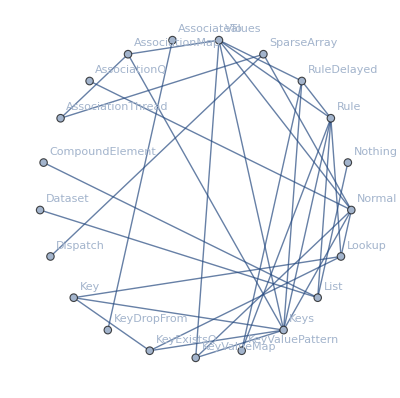
<|attributes→{HoldAllComplete,Protected},common option values→Missing[NotApplicable],date introduced→Day: Wed 9 Jul 2014,date last modified→Day: Wed 2 Mar 2016,dates modified→{Day: Wed 2 Mar 2016},documentation basic examples→{{An association in which key a is associated with value x, key b with value y, etc.:,<|a→x,b→y,c→z|>,∖[LeftAssociation]a→x,b→y,c→z∖[RightAssociation],Extract the value associated with key b:,%[b],y},{Convert a list of rules to an association:,Association[{a→x,b→y,c→z}],∖[LeftAssociation]a→x,b→y,c→z∖[RightAssociation],Convert an association to a list of rules:,Normal[<|a→x,b→y,c→z|>],{a→x,b→y,c→z}},{Keys are "transparent" for many operations:,Map[f,<|a→4,b→2,c→1,d→5|>],∖[LeftAssociation]a→f[4],b→f[2],c→f[1],d→f[5]∖[RightAssociation],Sort[<|a→4,b→2,c→1,d→5|>],∖[LeftAssociation]c→1,b→2,a→4,d→5∖[RightAssociation],Select[<|a→4,b→2,c→1,d→5|>,#>3&],∖[LeftAssociation]a→4,d→5∖[RightAssociation],Total[<|a→4,b→2,c→1,d→5|>],12,Position gives keys in an association:,Position[<|a→4,b→2,c→1,d→5|>,2],{{Key[b]}}},{Append to an association:,Append[<|a→x,b→y,c→z|>,d→w],∖[LeftAssociation]a→x,b→y,c→z,d→w∖[RightAssociation]},{Delayed rules can be used to construct associations whose values are stored unevaluated:,<|a:>(Print[z];1),b:>(Print[y];2),c:>(Print[z];3)|>,<|a→(Print[z];1),b→(Print[y];2),c→(Print[z];3)|>,The value in the association is evaluated when it is extracted:,%[b],y,2},{Values in associations can be extracted like parts:,<|a→x,b→y,c→z|>[[Key[b]]],y,If the key in an association is a string, no explicit Key is needed to extract it as a part:,<|a→x,b→y,c→z|>[[b]],y,Numerical part specifications work structurally on associations:,<|a→x,b→y,c→z|>[[2]],y,Lookups in associations interoperate with parts in lists and other expressions:,{<|a→x,b→{y,z}|>}[[1,Key[b],2]],z,The explicit Key can be omitted when the keys are strings:,{<|a→x,b→{y,z}|>}[[1,b,2]],z},{Keys extracts the list of keys:,Keys[<|a→x,b→y,c→z|>],{a,b,c}},{Associations can be modified by resetting values:,assoc=<|a→x,b→y,c→z|>,∖[LeftAssociation]a→x,b→y,c→z∖[RightAssociation],assoc[b]=w,w,assoc,∖[LeftAssociation]a→x,b→w,c→z∖[RightAssociation]}},documentation example counts→{BasicExamples→8,Scope→11,GeneralizationsExtensions→0,Options→0,Applications→0,PropertiesRelations→5,PossibleIssues→2,InteractiveExamples→0,NeatExamples→0},documentation example inputs→{BasicExamples→{{<|a→x,b→y,c→z|>,%[b]},{Association[{a→x,b→y,c→z}],Normal[<|a→x,b→y,c→z|>]},{Map[f,<|a→4,b→2,c→1,d→5|>],Sort[<|a→4,b→2,c→1,d→5|>],Select[<|a→4,b→2,c→1,d→5|>,#>3&],Total[<|a→4,b→2,c→1,d→5|>],Position[<|a→4,b→2,c→1,d→5|>,2]},{Append[<|a→x,b→y,c→z|>,d→w]},{<|a:>(Print[z];1),b:>(Print[y];2),c:>(Print[z];3)|>,%[b]},{<|a→x,b→y,c→z|>[[Key[b]]],<|a→x,b→y,c→z|>[[b]],<|a→x,b→y,c→z|>[[2]],{<|a→x,b→{y,z}|>}[[1,Key[b],2]],{<|a→x,b→{y,z}|>}[[1,b,2]]},{Keys[<|a→x,b→y,c→z|>]},{assoc=<|a→x,b→y,c→z|>,assoc[b]=w,assoc}},Scope→{{assoc=Association[Table[i→i^2,{i,10000}]];,assoc[10000]},{Keys[<|{2,3}→x,-Graphics-→y,<|a→1,b→2|>→z|>]},{<|a→x,b→y,c→z|>[d],Lookup[<|a→x,b→y,c→z|>,d,q]},{MatchQ[<|a→1|>,<|_→_|>],Replace[<|a→1|>,<|a→x_|>→x]},{<|1→2|>/.<|a_→b_|>→{a,b}},{f[<|1→2,3→4|>]/.f[<|a_→b_,___|>]→f[a,b]},{<|1→2,2→3,3→4,5→6|>/.<|___,3→b_,___|>→f[b]},{Cases[{<|1→x|>,<|1→x,2→y|>,<|1→x,2→y,3→z|>},<|_,_|>]},{g[<|k_→v_|>]:=v
g[<|1→2|>],h[<|k_→<|k2_->v2_|>|>]:={k,k2,v2}
h[<|1→<|2→3|>|>]},{MatchQ[<|a→1,b→2,c→3|>,KeyValuePattern[b→2]]},{Replace[<|a→1,b→2,c→3|>,KeyValuePattern[{a→x_,c→y_}]→{x,y}]}},GeneralizationsExtensions→{},Options→{},Applications→{},PropertiesRelations→{{Values[<|a→x,b→y,c→z|>],Keys[<|a→x,b→y,c→z|>]},{Normal[<|a→x,b→y,c→z|>]},{<|a→x,a→xp,b→y,c→z,c→zp|>,Join[<|a→x,b→y,c→z|>,<|a→xp,c→zp|>]},{v=w=<|a→1,b→2|>,v[a]=3,{v,w}},{<||>,Length[%]}},PossibleIssues→{{Level[<|a→x,b→y|>,{1}],Depth[<|a→x,b→y|>],Level[{a→x,b→y},{1}],Depth[{a→x,b→y}]},{ReplacePart[<|x→1,y→2|>,{0}→List],Normal[<|x→1,y→2|>]}},InteractiveExamples→{},NeatExamples→{}},documentation example text→{BasicExamples→{{An association in which key a is associated with value x, key b with value y, etc.:,Extract the value associated with key b:},{Convert a list of rules to an association:,Convert an association to a list of rules:},{Keys are "transparent" for many operations:,Position gives keys in an association:},{Append to an association:},{Delayed rules can be used to construct associations whose values are stored unevaluated:,The value in the association is evaluated when it is extracted:},{Values in associations can be extracted like parts:,If the key in an association is a string, no explicit Key is needed to extract it as a part:,Numerical part specifications work structurally on associations:,Lookups in associations interoperate with parts in lists and other expressions:,The explicit Key can be omitted when the keys are strings:},{Keys extracts the list of keys:},{Associations can be modified by resetting values:}},Scope→{{Associations work with any number of elements:,Extracting values from an association is highly efficient:},{Associations can have arbitrary expressions as keys, including associations:},{Missing elements are represented by Missing:,Lookup allows a default value to be given:},{Associations can be used for pattern matching:},{Extract key and value from an association:},{Replace arguments of a function:},{Pick the rule with the specific key:},{Filter associations with length 2 only:},{Define a function using an Association as an argument:,Use nested associations as a function argument:},{KeyValuePattern lets you match any element in an association:},{KeyValuePattern matches elements that appear anywhere in an association:}},GeneralizationsExtensions→{},Options→{},Applications→{},PropertiesRelations→{{Values extracts values from an association:,Keys extracts keys from an association:},{Normal turns an association into a list of rules:},{Associations keep only the last instance of repeated keys:},{When an association is modified, a new copy is created:,v is modified; w is unchanged:},{Associations can have zero length:}},PossibleIssues→{{Association counts as one level, not two, in structural functions:,Lists of rules are two levels:},{Replacing the head of an Association loses keys:,Extract rules from an Association:}},InteractiveExamples→{},NeatExamples→{}},eponymous people→{},equal-precedence symbols→Missing[NotApplicable],external links→{Fast Introduction for Programmers: Associations→http://www.wolfram.com/language/fast-introduction-for-programmers/associations/},frequencies of usage→{All→0.00013705,StackExchange→0.000903852,TypicalProductionCode→8.58331×10^-6,WolframAlphaCodebase→3.1818×10^-6,WolframDemonstrations→0.,WolframDocumentation→0.00238174},full version introduced→10,full version last modified→10.4,full versions modified→{10.4},functionality areas→{AssociationSymbols},symbol background→Missing[NotAvailable],keyboard shortcuts→Missing[NotAvailable],link trails→{{guide/WolframRoot,guide/Associations,ref/Association},{guide/WolframRoot,guide/FunctionalProgramming,guide/Associations,ref/Association},{guide/WolframRoot,guide/ListManipulation,guide/Associations,ref/Association}},memberships→{Wolfram Language atomic functions},name→Association,option names→{},options→{},plaintext usage→Association[key1->val1, key2->val2, …] or ∖[LeftAssociation]key1->val1, key2->val2, …∖[RightAssociation] represents an association between keys and values.,precedence ranks→Missing[NotApplicable],ranks of usage→{All→210,StackExchange→104,TypicalProductionCode→1016,WolframAlphaCodebase→662,WolframDemonstrations→4876,WolframDocumentation→33},related entities→Missing[NotAvailable],related guide pages→{Computation with Structured Datasetspaclet:guide/ComputationWithStructuredDatasets,Associationspaclet:guide/Associations,Summary of New Features in 10paclet:guide/SummaryOfNewFeaturesIn100,New in 10.0: Core Language & Structurepaclet:guide/NewIn100CoreLanguageAndStructure,Automated Reportspaclet:guide/AutomatedReports,WDF (Wolfram Data Framework)paclet:guide/WDFWolframDataFramework,Summary of New Features in 10.4paclet:guide/SummaryOfNewFeaturesIn104,New in 10.0: Core Languagepaclet:guide/NewIn100CoreLanguage,Language Overviewpaclet:guide/LanguageOverview,Setting Up Input Interpreterspaclet:guide/InterpretingStrings,Wolfram Language Syntax Characterspaclet:guide/WolframLanguageSyntaxCharacters,Expressionspaclet:guide/Expressions,WDFpaclet:guide/WDF,Scientific Data Analysispaclet:guide/ScientificDataAnalysis,Wolfram Data Repositorypaclet:guide/WolframDataRepository},related symbols→{List,Dataset,Normal,AssociationQ,Lookup,KeyExistsQ,Keys,Values,KeyValuePattern,SparseArray,CompoundElement},relationship community graph→-Graphics-,relationship graph→-Graphics-,short notations→{∖[LeftAssociation]…∖[RightAssociation]},subject classifications→Missing[NotAvailable],symbols using as attribute→{},symbols using as option→{},text strings→{Association[Subscript[key, 1]→Subscript[val, 1],Subscript[key, 2]→Subscript[val, 2],…] or ∖[LeftAssociation]Subscript[key, 1]→Subscript[val, 1],Subscript[key, 2]→Subscript[val, 2],…∖[RightAssociation] 
represents an association between keys and values.,The value associated with a given key can be extracted using assoc[key].,An Association acts like a symbolically indexed list. The value associated with a given key can be extracted by using the part specification Key[key]. If key is a string, Key can be omitted.,If key is not present in assoc, assoc[key] yields Missing["KeyAbsent",key].,Typical list operations (such as Map, Select, and Sort) apply to the values in an association, leaving the keys unchanged.,Association[{Subscript[key, 1]->Subscript[val, 1],…}] gives <|Subscript[key, 1]->Subscript[val, 1],…|>.,If there are multiple elements with the same key, all but the last of these elements are dropped. Merge yields instead a list of values for repeated keys.,Association can be input using the characters ∖[LeftAssociation] and ∖[RightAssociation].,Normal converts an Association to a list of rules.,KeyValuePattern can be used to represent a pattern for associations that include particular elements.,An association in which key a is associated with value x, key b with value y, etc.:,Extract the value associated with key b:,Convert a list of rules to an association:,Convert an association to a list of rules:,Keys are "transparent" for many operations:,Position gives keys in an association:,Append to an association:,Delayed rules can be used to construct associations whose values are stored unevaluated:,The value in the association is evaluated when it is extracted:,Values in associations can be extracted like parts:,If the key in an association is a string, no explicit Key is needed to extract it as a part:,Numerical part specifications work structurally on associations:,Lookups in associations interoperate with parts in lists and other expressions:,The explicit Key can be omitted when the keys are strings:,Keys extracts the list of keys:,Associations can be modified by resetting values:,Associations work with any number of elements:,Extracting values from an association is highly efficient:,Associations can have arbitrary expressions as keys, including associations:,Missing elements are represented by Missing:,Lookup allows a default value to be given:,Associations can be used for pattern matching:,Extract key and value from an association:,Replace arguments of a function:,Pick the rule with the specific key:,Filter associations with length 2 only:,Define a function using an Association as an argument:,Use nested associations as a function argument:,KeyValuePattern lets you match any element in an association:,KeyValuePattern matches elements that appear anywhere in an association:,Values extracts values from an association:,Keys extracts keys from an association:,Normal turns an association into a list of rules:,Associations keep only the last instance of repeated keys:,When an association is modified, a new copy is created:,v is modified; w is unchanged:,Associations can have zero length:,Association counts as one level, not two, in structural functions:,Lists of rules are two levels:,Replacing the head of an Association loses keys:,Extract rules from an Association:},timeline→-Graphics-,timeline events→Interval[{Day: Wed 9 Jul 2014,Day: Wed 2 Mar 2016}]Association,translations→{Simplified Chinese→关联,Traditional Chinese→關聯,French→association,German→Assoziation,Greek→σύνδεσμος κλειδιών-αξιών,Japanese→連想,Korean→연상,Lithuanian→asociacija,Polish→stowarzyszenie,Portuguese→associação,Russian→ассоциация,Spanish→asociación,Ukrainian→асоціація,Vietnamese→sự kết hợp},typeset usage→Association[key_1→val_1,key_2→val_2,…] or ∖[LeftAssociation]key_1→val_1,key_2→val_2,…∖[RightAssociation] represents an association between keys and values.,URL→http://reference.wolfram.com/language/ref/Association.html,version introduced→10,version last modified→10.4,versions modified→{10.4},Wolfram documentation link→Associationpaclet:ref/Association|>

```mathematica
Entity["WolframLanguageSymbol","Association"]["PropertyAssociation"]
```

EntityPropertyAssociation

```mathematica
EntityValue[
	EntityClass["Country", "GroupOf8"],
	{"Population", "MedianAge", "LandArea"},
	"EntityPropertyAssociation"
]
```

<|Canada→<|Population→35949709 people,MedianAge→39.685 yr,LandArea→3.51102×10^6 mi^2|>,France→<|Population→64457201 people,MedianAge→40.027 yr,LandArea→212345. mi^2|>,Germany→<|Population→81707789 people,MedianAge→44.279 yr,LandArea→134623. mi^2|>,Italy→<|Population→59504212 people,MedianAge→43.294 yr,LandArea→113568. mi^2|>,Japan→<|Population→127974958 people,MedianAge→44.862 yr,LandArea→144689. mi^2|>,Russia→<|Population→143888004 people,MedianAge→38.005 yr,LandArea→1999236083984375/316160658 mi^2|>,United Kingdom→<|Population→65397080 people,MedianAge→39.779 yr,LandArea→93409.7 mi^2|>,United States→<|Population→319929162 people,MedianAge→37.064 yr,LandArea→3.53744×10^6 mi^2|>|>

Dataset:

```mathematica
EntityValue[
	EntityClass["Country", "GroupOf8"],
	{"Population", "MedianAge", "LandArea"},
	"Dataset"
]
```

Dataset[<>]

## Association: Performance

There are a couple downsides to using Association objects.

Creating Association objects can be slow:

```mathematica
keys=ToString/@Range[10^6];
values=Range[10^6];
assoc = AssociationThread[keys, values];//AbsoluteTiming
```

{0.634472,Null}

Association objects use more memory:

```mathematica
ByteCount[{keys, values}]
ByteCount[assoc]
```

48000280

142458984

On the other hand, appending elements to an association is much faster than appending elements to a List object:

```mathematica
makeAssociation[n_]:=Module[{tmp=<||>},
Do[AppendTo[tmp, i->i], {i,n}];
tmp
]
```

Check output:

```mathematica
makeAssociation[10]
```

<|1→1,2→2,3→3,4→4,5→5,6→6,7→7,8→8,9→9,10→10|>

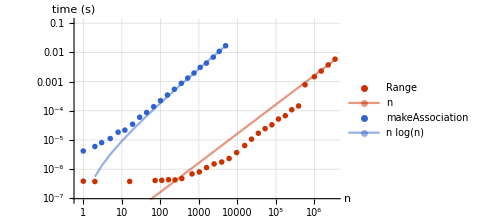

```mathematica
Needs["GeneralUtilities`"]
BenchmarkPlot[{Range, makeAssociation}, Identity, "IncludeFits"->True]
```

Recall that the List variation earlier had n^2 timing, corresponding to a O(n) timing for appending a single element. The corresponding time for appending a single element to an association scales as O(log n).

Finally, we have already seen that looking up values associated with a Key is extremely fast.

## Association: Summary

Excellent for quickly retrieving values associated to keys.

Excellent timing performace for inserting, deleting, appending etc.

Many special functions designed to work with s objects.

Memory usage can be high.